```mathematica
Clear["Global`*"]
```

## Операция с дробями

```mathematica
t=(a+b)^2/((a-b)(a+2b)^2)
```

(a+b)^2/((a-b) (a+2 b)^2)

```mathematica
Expand[t]
```

a^2/((a-b) (a+2 b)^2)+(2 a b)/((a-b) (a+2 b)^2)+b^2/((a-b) (a+2 b)^2)

```mathematica
u =Apart[t]
```

-4/(9 (-a+b))+a/(6 (a+2 b)^2)+7/(18 (a+2 b))

```mathematica
Together[u]
```

(a^2+2 a b+b^2)/((a-b) (a+2 b)^2)

```mathematica
Factor[u]
```

(a+b)^2/((a-b) (a+2 b)^2)

```mathematica
Simplify[u]
```

(a+b)^2/((a-b) (a+2 b)^2)

```mathematica
v=1/(3 (1+x))-(-1+2 x)/(6 (1-x+x^2))+2/(3 (1+1/3 (-1+2 x)^2));
Simplify[v]
Factor[v]
```

1/(1+x^3)

1/((1+x) (1-x+x^2))

## Операция с многочленами

```mathematica
u=(a+b)^3
```

(a+b)^3

```mathematica
v= Expand[u]
```

a^3+3 a^2 b+3 a b^2+b^3

```mathematica
Factor[v]
```

(a+b)^3

```mathematica
Collect[u,a]
```

a^3+3 a^2 b+3 a b^2+b^3

```mathematica
Collect[(1+x+3y)^4,x]
```

1+x^4+12 y+54 y^2+108 y^3+81 y^4+x^3 (4+12 y)+x^2 (6+36 y+54 y^2)+x (4+36 y+108 y^2+108 y^3)

```mathematica
Expand[(1+x+3y)^4]
```

1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4

## Тригонометрия

```mathematica
Expand[Sin[2x],Trig->True]
```

2 Cos[x] Sin[x]

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

```mathematica
TrigReduce[2 Cos[x] Sin[x]]
```

Sin[2 x]

## График функции одной переменной

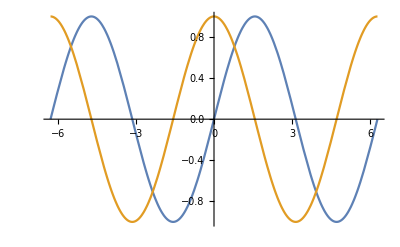

```mathematica
f=Sin[x];
g=Cos[x];
Plot[{f,g},{x,-2Pi,2Pi}]
```

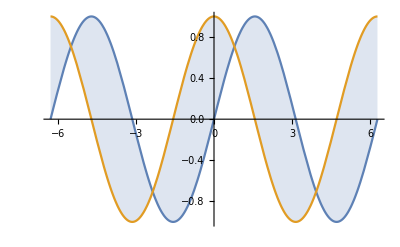

```mathematica
f=Sin[x];
g=Cos[x];
Plot[{f,g},{x,-2Pi,2Pi},Filling->{1->{2}}]
```

## Точечный график

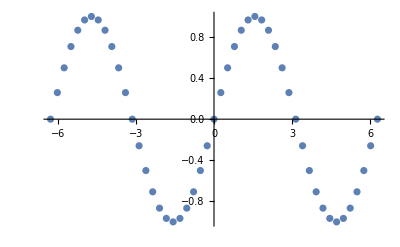

```mathematica
x=Table[i,{i,-2π,2π,π/12}];
y =Table[Sin[i],{i,-2π,2π,π/12}];
ListPlot[Transpose[{x,y}]]
```

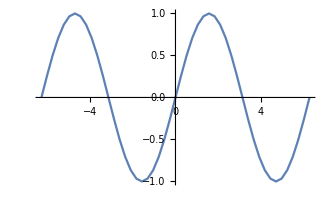

```mathematica
ListLinePlot[Transpose[{x,y}]]
```

## Параметрический график

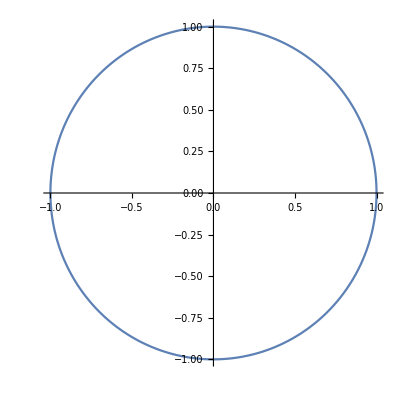

```mathematica
ParametricPlot[{Sin[t],Cos[t]},{t,0,2Pi}]
```

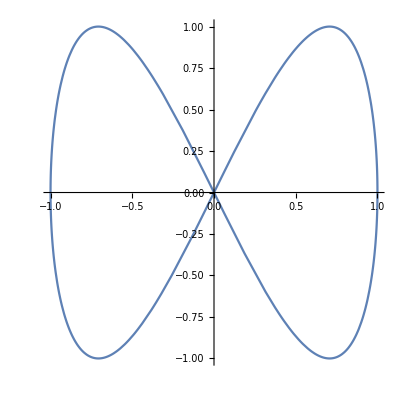

```mathematica
ParametricPlot[{Sin[t],Sin[2t]},{t,0,2Pi}]
```

## График уравнения

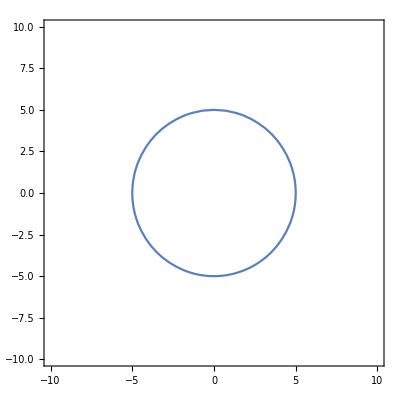

```mathematica
ContourPlot[x^2+y^2==25,{x,-10,10},{y,-10,10}]
```

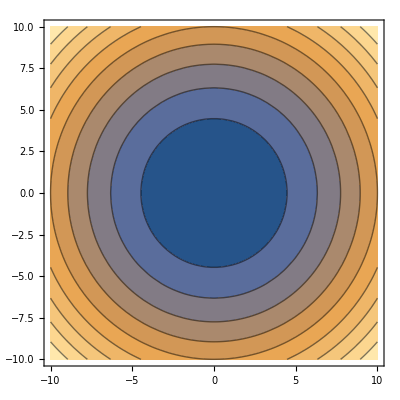

```mathematica
ContourPlot[x^2+y^2,{x,-10,10},{y,-10,10}]
```

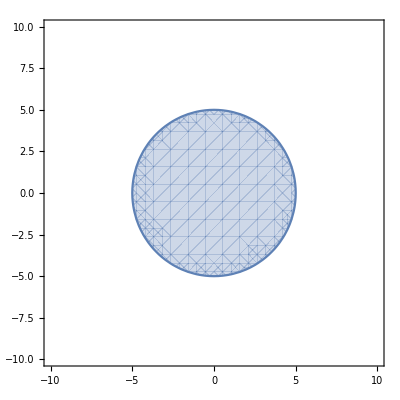

```mathematica
RegionPlot[x^2+y^2<25,{x,-10,10},{y,-10,10}]
```

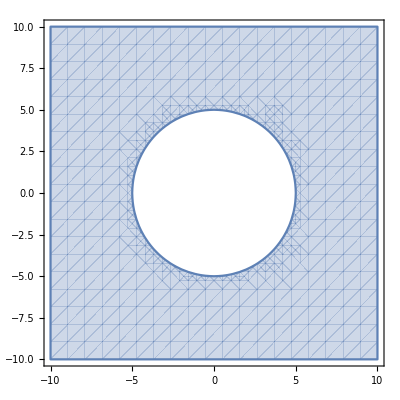

```mathematica
RegionPlot[x^2+y^2>25,{x,-10,10},{y,-10,10}]
```

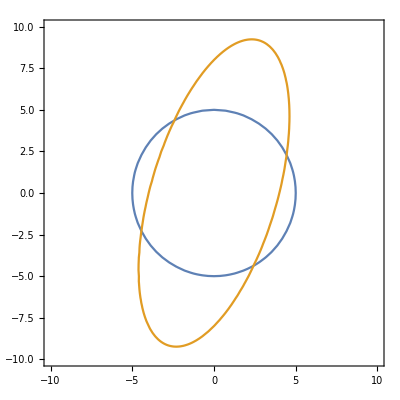

```mathematica
ContourPlot[{x^2+y^2==25, 4x^2-2x y+y^2==64},{x,-10,10},{y,-10,10}]
```

## Объединение графиков

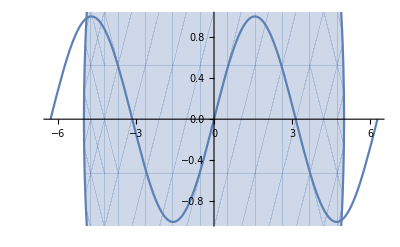

```mathematica
Show[
Plot[Sin[x],{x,-2Pi,2Pi}],
RegionPlot[x^2+y^2<25,{x,-10,10},{y,-10,10}]
]
```

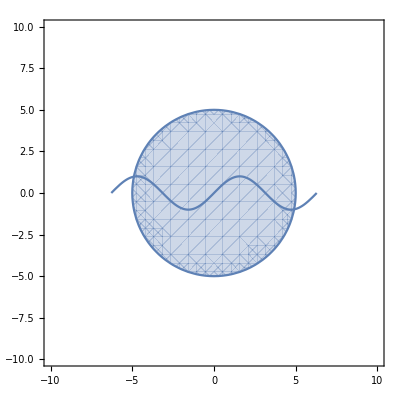

```mathematica
Show[
RegionPlot[x^2+y^2<25,{x,-10,10},{y,-10,10}],
Plot[Sin[x],{x,-2Pi,2Pi}]
]
```

## Трехмерный график

```mathematica
Plot3D[Sin[x]Cos[y],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2+y^2+z^2==16,{x,-5,5},{y,-5,5},{z,-5,5},RegionFunction->Function[{x,y,z},x<0||y>0],RegionBoundaryStyle->None]
```

-Graphics3D-

## Производные

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=Sin[x]Cos[x]
D[f[x],x]
```

Cos[x]^2-Sin[x]^2

```mathematica
D[f[x],x]/.x->Pi/6
```

1/2

```mathematica
D[f[xt],xt]
```

Cos[xt]^2-Sin[xt]^2

```mathematica
D[f[xt],t]
```

0

```mathematica
f[xt]
```

Cos[xt] Sin[xt]

```mathematica
f[x_,y_]:=Sin[x]Cos[y]
D[f[x,y],x]
D[f[x,y],y]
D[f[x,y],x,y]
```

Cos[x] Cos[y]

-Sin[x] Sin[y]

-Cos[x] Sin[y]

### производная через штрих

```mathematica
Clear["Global`*"]
```

```mathematica
g[x_]:=Sin[x]Cos[x]^2
g'[x]
```

Cos[x]^3-2 Cos[x] Sin[x]^2

```mathematica
g''[x]
```

-7 Cos[x]^2 Sin[x]+2 Sin[x]^3

```mathematica
g''''[x]
```

61 Cos[x]^2 Sin[x]-20 Sin[x]^3

```mathematica
g'[π/6]
```

(√3)/8

## Дифференциал

```mathematica
Clear["Global`*"]
```

```mathematica
Dt[a x+b, x]
```

a+x Dt[a,x]+Dt[b,x]

```mathematica
D[a x+b, x]
```

a

## Интеграл

### неопределенный интеграл

```mathematica
Integrate[Sin[x]Cos[x],x]
```

-1/2 Cos[x]^2

```mathematica
z= Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
Simplify[D[z,x]]
```

1/(1+x^3)

```mathematica
Log[Exp[1]]
```

1

### определенный интеграл

```mathematica
Integrate[1/(x^3+1),{x,0,10}]
```

1/18 (√3 π+6 √3 ArcTan[19/(√3)]+3 Log[121/91])

```mathematica
Integrate[1/(x^3+1),{x,0,10}]//N
```

1.2042

1/(1+x^3)

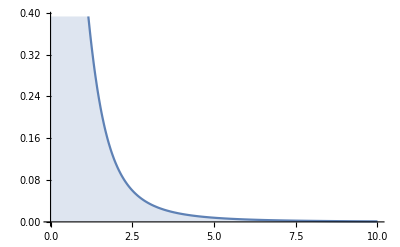

```mathematica
z = 1/(x^3+1)
Plot[z,{x,0,10},Filling->0]
```

```mathematica
f = 1/(x^4+x^2+1);
Integrate[f,{x,-∞,∞}]
```

π/(√3)

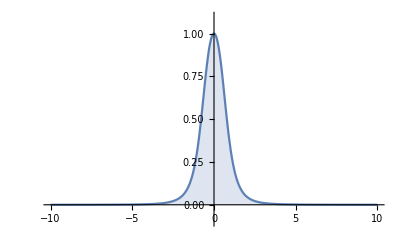

```mathematica
Plot[f,{x,-10,10},Filling->0,PlotRange->{-0.1,1.1}]
```